1.04625

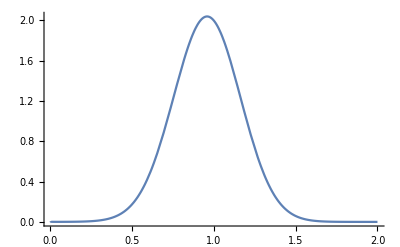

-Graphics3D-

-Graphics3D-

```mathematica
m=1;
s=0.2;
psir=Exp[-(r-m)^2/(2 s^2)]/(r s √(2 π));
dpsir=D[psir,r];
psi[x_,y_]:=psir/.r->√(x^2+y^2);
dpsi[x_,y_]:=dpsir/.r->√(x^2+y^2);
a=1;
pr=2a;
NIntegrate[a^-1*psir/.{r->a^-1*t},{t,10^-3,a+pr}]
Plot[a^-1*psir/.{r->a^-1*t},{t,10^-3,pr},PlotRange->All]
Plot3D[a^-1*psi[a^-1 x,a^-1 y],{x,-pr,pr},{y,-pr,pr},PlotRange->All,ColorFunction->"TemperatureMap",PlotPoints->50]
Plot3D[a^-1 dpsi[a^-1 x,a^-1 y],{x,-pr,pr},{y,-pr,pr},PlotRange->All,ColorFunction->"TemperatureMap",PlotPoints->50]
```

0.693147

0.693147

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.28117 and 0.00302702 for the integral and error estimates.

6.28117

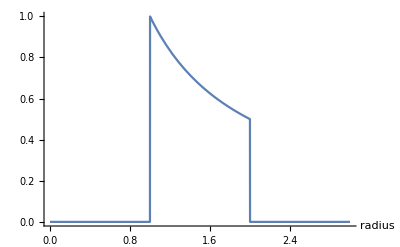

-Graphics3D-

```mathematica
radius=1.5;
thickness=0.5;
psir=If[r>10^-16,HeavisideTheta[thickness^2-(r-radius)^2]/r,0.0];
psi=psir/.r->√(x^2+y^2);
pr=1;
Integrate[1/r,{r,radius-thickness,radius+thickness}]
NIntegrate[psir,{r,radius-thickness,radius+thickness}]
NIntegrate[psi,{x,-radius-thickness,radius+thickness},{y,-radius-thickness,radius+thickness}]
Plot[psir,{r,radius-thickness-pr,radius+thickness+pr},AxesLabel->{"radius"},PlotRange->All]
RevolutionPlot3D[psir,{r,radius-thickness-pr,radius+thickness+pr},ColorFunction->"TemperatureMap",PlotRange->All,PlotPoints->50]
```

```mathematica
a=1;
NIntegrate[a^-1(√(x^2+y^2))^-1 Exp[-(a^-1 √(x^2+y^2)-m)^2/(2 s^2)]/(s √(2 π)),{x,a(-m-3s),a(m+3s)},{y,a(-m-3s),a(m+3s)}]
NIntegrate[a^-2 Exp[-(a^-1 √(x^2+y^2)-m)^2/(2 s^2)]/(s √(2 π)),{x,a(-m-3s),a(m+3s)},{y,a(-m-3s),a(m+3s)}]
N[2π]
```

6.28067

6.27896

6.28319

```mathematica
img=Image[Graphics[{EdgeForm[{Thickness[0.03],Black}],White,Rectangle[{2,1}],EdgeForm[{Thickness[0.03],Black}],White,Triangle[{{2,2.8},{2,3.8},{3,2.8}}],{Thickness[0.03],Black,Circle[{2,2},0.4]},{Thickness[0.03],Black,Circle[{4,2.2},0.8]}},ImageSize->200]]
f=Map[1.0-Total[#]/N[255*3]&,ImageData[img,"Byte"],{2}];
```

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]];
Export["f.tsv",f, "Table"]
```

f.tsv

```mathematica
(*SetDirectory[NotebookDirectory[]];
wf=Import["wf.ssv","Table"];
min=Min@Flatten@wf;
diff=Max@Flatten@wf-minwf;
nwf=Map[1.0-(#-min)/diff&,wf,{2}];
Image[nwf]*)
```

```mathematica
rs=First@Import["r.ssv","Table"];
rbeg=First@rs;rend=Last@rs; rstep=rs⟦2⟧-rbeg; 
rtoi[r_]:=(r-rbeg)/rstep+1;
wfs=SequenceSplit[Import["wfs.ssv","Table"],{{}}];
wwfs=SequenceSplit[Import["wwfs.ssv","Table"],{{}}];
nwfs=Map[
With[{min=Min@Flatten@#,diff=Max@Flatten@#-Min@Flatten@#},Map[1.0-(#-min)/diff&,#,{2}]]&,
wfs];
nwwfs=Map[
With[{min=Min@Flatten@#,diff=Max@Flatten@#-Min@Flatten@#},Map[1.0-(#-min)/diff&,#,{2}]]&,
wwfs];
wimgs=Map[Image@#&,nwfs];
wwimgs=Map[Image@#&,nwwfs];
Manipulate[{wimgs⟦rtoi[r]⟧,wwimgs⟦rtoi[r]⟧},{r,rbeg,rend,rstep}]
```

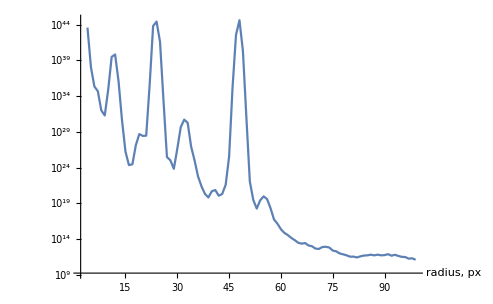

```mathematica
intnwfs=MapThread[{#1,Total@Flatten@#2}&,{rs,wfs}];
ListLinePlot[intnwfs,PlotRange->All,ScalingFunctions->"Log",AxesLabel->{"radius, px"}]
```

```mathematica
combineFields[rs_]:=Total@Map[nwwfs⟦rtoi[#]⟧&,rs]-1.0;
Image[combineFields[{24,48}]]
```

-Graphics-

```mathematica
cnwwfss=Table[Map[If[#>t,1.0,#]&,nwwfs,{3}],{t,0.0,1.0,0.1}];
cwwimgss=Map[Image@#&,cnwwfss,{2}];
Manipulate[cwwimgss⟦t,rtoi[r]⟧,{t,1,Length@cwwimgss,1},{r,rbeg,rend,rstep}]
```